# 29: Shifted QR Algorithm

This (with some bells and whistles) is what almost all dense eigenvalue algorithms are based on after a preliminary reduction to upper Hessenberg (tridiagonal for symmetric) form. We are going to look at the scheme first and then work out why it works.

Real world versions of QR eigenvalue algorithms do more than one shift at a time and these shifts are implemented implicitly.

## Single Shift

We implemented a single shift μ_1as follows
	H | - | μ_1 I | = | Q_1.R_1 |   |  
  |   | H_1 | = | R_1.Q_1 | + | μ_1 I

Remember this QR step does not change the eigen values since
	  | H-μ_1 I | = | Q_1.R_1
⟹ | (Q_1)ᵀ.(H-μ_1 I) | = | R_1
⟹ | (Q_1)ᵀ.(H-μ_1 I).Q_1 | = | R_1.Q_1
⟹ | (Q_1)ᵀ.(H-μ_1 I).Q_1 | = | H_1-μ_1 I
In words, the single shift QR algorithm implements an orthogonal similarity transformation of H-μ_1 I. This is the same as implementing the same similarity transformation (defined by Q_1) on H
	  | (Q_1)ᵀ.(H-μ_1 I).Q_1 | = | H_1-μ_1 I
⟹ | (Q_1)ᵀ.H.Q_1-μ_1(Q_1)ᵀ.Q_1 | = | H_1-μ_1 I
⟹ | (Q_1)ᵀ.H.Q_1 | = | H_1
All we really need is Q_1!

There are several ways to compute Q_1. In exact arithmetic they must all be "essentially" the same since the QR decomposition is "essentially" unique.  Of course, we know some are more stable than others. Some are more work than others!

For instance we can compute all of Q (using say a QR decomposition) before we start doing anything else or we could do the columns (and matching rows) with tiny Given’s rotations one at a time and accumulate Q.  This version can efficiently exploit T being tridiagonal.  It results in a sequence of tiny computations.  The common efficient implementation does not actually construct Q! It simply computes the first column of Q and then directly computes H_1 using a sequence of tiny orthogonal matrices place to restore a Hessenberg matrix with a bulge to Hessenberg form.  This implicit Hessenberg process gives the same result as the explicit computation by the “Unique Q” theorem.

The implicit computation is called an implicit shift and it is much less work when we try to do two (or more) shifts at the same time.

## Double Shift

Double shifts are vitally important for real but non-symmetric matrices because of the complex eigenvalue pairs.  A single real shift can not approximate a complex conjugate eigen pair!  To work out how to do this we need to manually work through two steps of QR to see what is actually happening
	H | - | μ_1 I | = | Q_1.R_1 |   |  
  |   | H_1 | = | R_1.Q_1 | + | μ_1 I
H_1 | - | μ_2 I | = | Q_2.R_2 |   |  
  |   | H_2 | = | R_2.Q_2 | + | μ_2 I

Remember each QR step does not change the eigen values since
	  | H-μ_1 I | = | Q_1.R_1
⟹ | (Q_1)ᵀ.(H-μ_1 I) | = | R_1
⟹ | (Q_1)ᵀ.(H-μ_1 I).Q_1 | = | R_1.Q_1
⟹ | (Q_1)ᵀ.(H-μ_1 I).Q_1 | = | H_1-μ_1 I
and for the same reasons
	(Q_2)ᵀ.(H_1-μ_2 I).Q_2 | = | H_2-μ_2 I.

The question is what does this look like if we try to combine the two steps. One way to think about this would be to look at the combined orthogonal matrices Q=Q_1.Q_2 (still orthogonal) and the combined upper triangular matrices R=R_2.R_1(still upper triangular)   
	Q.R=(Q_1.Q_2).(R_2.R_1)
A direct computation gives 
	  | (Q_1.Q_2).(R_2.R_1) | = | Q_1.(Q_2.R_2).R_1
⟹ |   | = | Q_1.(H_1-μ_2 I).R_1
⟹ |   | = | Q_1.((R_1.Q_1 | + | μ_1 I)-μ_2 I).R_1
⟹ |   | = | (Q_1.R_1.Q_1+(μ_1-μ_2)Q_1).R_1
⟹ |   | = | (Q_1.R_1+(μ_1-μ_2)I).Q_1.R_1
⟹ |   | = | ((H-μ_1 I)+(μ_1-μ_2)I).(H-μ_1 I)
⟹ |   | = | (H-μ_2 I).(H-μ_1 I)
In words, the effect of the double step with the two shifts is described by the matrix quadratic
	(H-μ_2 I).(H-μ_1 I)
which is real if μ_1 are the roots of a real polynomial or eigenvalues of a real matrix!  It should be possible to do the double step in real arithmetic if μ_1 and μ_2 are real (no surprise there) or a complex conjugate pair!

We could build the matrix (H-μ_2 I).(H-μ_1 I), compute a QR decomposition of it and reverse the order but we do not need to.  The implicit Q theorem says that although there are many different Hessenberg reductions of a matrix A ones with the same first column are the same if we make sure we have positive subdiagonals. So the first column of Q and the input H determines the new Hessenberg form.

## Implicit Shifts

### M trick

The first column of (H-μ_2 I).(H-μ_1 I)=H^2-(μ_1+μ_2)H+μ_1 μ_2 I is simply m=(H-μ_2 I).(H-μ_1 I).e_1.  Since H is Upper Hessenberg m has three non-zero entries at the top. A direct computation gives
	m_1 | = | H_(1,1)H_(1,1) | + | H_(1,2)H_(2,1) | - | s H_(1,1) | + | t
m_2 | = | H_(2,1)H_(1,1) | + | H_(2,2)H_(2,1) | - | s H_(2,1) |   |  
m_3 | = | H_(3,2)H_(2,1) |   |   |   |   |   |      
where s=μ_1+μ_2 and t=μ_1 μ_2 are real.

### Shift Trick

As an added bonus if we are using shifts μ_1 and μ_2 which are eigenvalues of a 2×2 matrix 
	S=(S_(1,1) | S_(1,2)
S_(2,1) | S_(2,2))
we do not need to compute eigenvalues since 
	t=μ_1 μ_2=Det(S)=S_(1,1)S_(2,2)-S_(1,2)S_(2,1)
and
	s=μ_1+μ_2=tr(S)=S_(1,1)+S_(2,2).

### Implicit Trick

We could:

Form M=(H-μ_2 I).(H-μ_1 I)

Compute the QR decomposition of M

Flip the order to get R.Q

The cool thing is that we do not need to:  there is a much faster way!

All we really want out of the shifts etc is the orthogonal matrix Q: We do not care about M or R.  Even better all we really want to do with Q is form the Hessenberg decomposition (similarity transformation) Q.H.Qᵀ.  The Implicit Q theorem says everything we want is determined by the first column of Q!

The Implicit Shift Trick consists of: Starting from an Upper Hessenberg matrix H and two shifts μ1and μ2

Compute m=M⟦All,1⟧={m_1,m_2,m_3,0,…,0}

Compute the Householder Reflector Q_0 satisfying (Q_0)ᵀ.m=e_1

Note that Q_0.e_1=m.  In other words the first column of Q_0 contains our target.

Note that Q_0.H recombines the first three rows of H

Note that H.(Q_0)ᵀ recombines the first three columns of H

Compute Q_0.H.(Q_0)ᵀ and note it is almost Upper Hessenberg

The only problem is that the top 4×34 block has been filled in.

This is called a bulge!

We will see later how to push the bulge down to the bottom.

Lets look at a picture of this “cast of characters”.

```mathematica
SetOptions[MatrixPlot, ColorRules->{0->LightGreen}];
m=12;Id=IdentityMatrix[m];
A=RandomReal[{-1,1},{m,m}];
H=HessenbergDecomposition[A]⟦2⟧;
HBot=H⟦m-1;;m,m-1;;m⟧;
{s,t}={Tr[HBot],Det[HBot]};
{μ1,μ2}=Eigenvalues[HBot];
M=Chop[(H- μ1 Id).(H-μ2 Id)];
m1Top={
H⟦1,1⟧^2+H⟦1,2⟧ H⟦2,1⟧- s H⟦1,1⟧+t,
H⟦2,1⟧ H⟦1,1⟧+H⟦2,2⟧ H⟦2,1⟧- s H⟦2,1⟧,
H⟦3,2⟧ H⟦2,1⟧
};
v0=m1Top; v0⟦1⟧+=Norm[m1Top];v0=Normalize[v0];
Q0=SparseArray[Band[{1,1}]->1,{m,m}]; Q0⟦1;;3,1;;3⟧-=2 KroneckerProduct[v0,v0];
TabView[{
"M"->MatrixPlot[Chop[M]],
"Q0"->MatrixPlot[Chop[Q0]],
"H"->MatrixPlot[Chop[H]],
"Q0ᵀ.M"->MatrixPlot[Chop[Q0ᵀ.M]],
"Q0.H"->MatrixPlot[Chop[Q0.H]],
"Q0.H.Q0ᵀ"->MatrixPlot[Chop[Q0.H.Q0ᵀ]],
"Q0 & M"->TableForm[
{m1Top,M⟦1;;3,1⟧,Q0⟦1;;3,1⟧,Q0⟦1;;3,1⟧/M⟦1;;3,1⟧},
TableHeadings->{{"m1Top","M⟦1;;3,1⟧","Q0⟦1;;3,1⟧","(Q0/M)⟦1;;3,1⟧"},Automatic}]}]
```

1234567

All we have to do is move the bulge down to the bottom (using orthogonal similarity transformations and we have completed a “double-shifted Wilkinson shift QR iteration”.  Remember the Hessenberg decomposition is unique given the first column of Q.  We matched the first column of Q so we get the same output as doing the shifts twice using complex arithmetic.  It may not be a free lunch but it is a really good lunch special.

## Bulge Chasing

To restore Q_0.H.(Q_0)ᵀ to Hessenberg form we need to chase a 4×4 bulge from the top of an m×m matrix down to the bottom. This is just a sequence of tiny versions of our Hessenberg code.

Move all the mass below the diagonal in the first column onto the subdiagonal entry with a tiny 3×3 orthogonal Q_1

We are going to use a tiny standard Householder

Compute Q_1.Q_0H.(Q_1.Q_0)ᵀ=Q_1.(Q_0 H.(Q_0)ᵀ.(Q_1)ᵀ which now has an upper Hessenberg first column and a bulge that has moved down by one.

Simply repeat till the bulge gets to the bottom then finish the “chase” off with a 2×2 orthogonal.

If you need the eigenvectors you can accumulate them.  It is common to do the updating in place

### Manual

First we create a bulge explicitly building Q0 and make sure we remember that it is much more efficient not to do this stuff implicitly.

Just a demo of implict vs explicit!

```mathematica
m=12;
Id=SparseArray[Band[{1,1}]->1,{m,m}]; 
H=HessenbergDecomposition[RandomReal[{-1,1},{m,m}]]⟦2⟧;
(* Create the bulge *)
(* Compute the Shifts and the first colun of M *)
HBot=H⟦m-1;;m,m-1;;m⟧;{s,t}={Tr[HBot],Det[HBot]};
m1Top={
H⟦1,1⟧^2+H⟦1,2⟧ H⟦2,1⟧- s H⟦1,1⟧+t,
H⟦2,1⟧ H⟦1,1⟧+H⟦2,2⟧ H⟦2,1⟧- s H⟦2,1⟧,
H⟦3,2⟧ H⟦2,1⟧
};
(* Explicitly create the bulge using the Householder Q0  *)
v0=m1Top; v0⟦1⟧+=Norm[m1Top];v0=Normalize[v0];
Q0=Id;Q0⟦1;;3,1;;3⟧-=2 KroneckerProduct[v0,v0];
HExp=Q0.H.Q0ᵀ;
(* Implicitly create the bulge using v0 *)
HImp=H; 
HImp⟦1;;3,All⟧-=2KroneckerProduct[v0,v0.HImp⟦1;;3,All⟧];
HImp⟦All,1;;3⟧-=2KroneckerProduct[HImp⟦All,1;;3⟧.v0,v0];
(* Check they are the same *)
Norm[HImp-HExp]
```

I think the implicit versions is clearer and easier to code! It definitely runs faster! From now on we are doing implicit updates in-place on H.

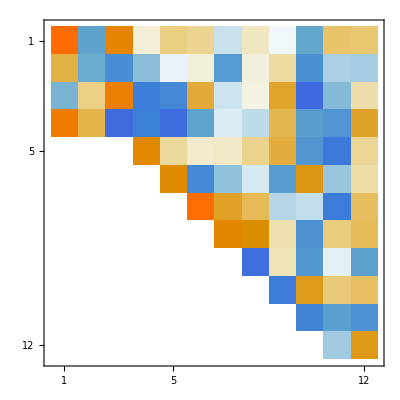
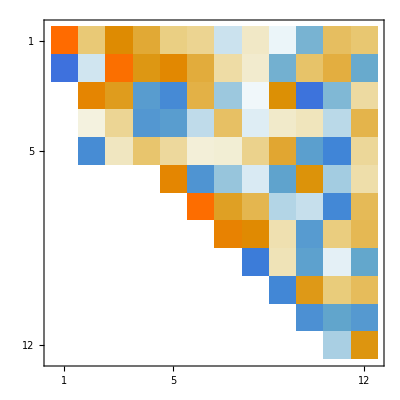
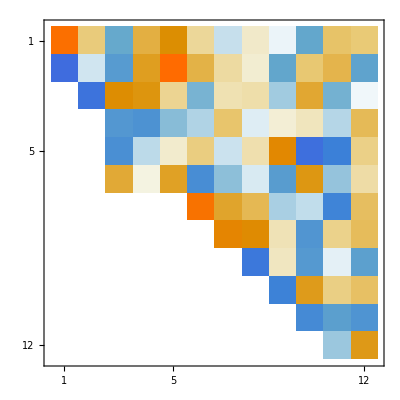
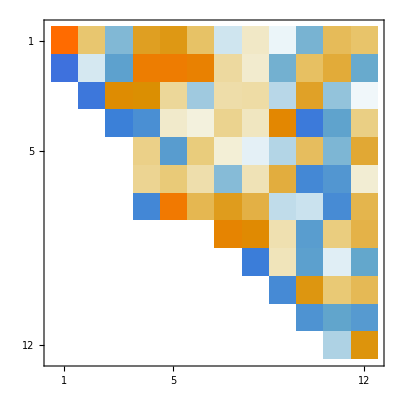

```mathematica
m=12;
Id=SparseArray[Band[{1,1}]->1,{m,m}]; 
H=HessenbergDecomposition[RandomReal[{-1,1},{m,m}]]⟦2⟧;
H0=H;
(* Create the bulge *)
(* Compute the Shifts and the first colun of M *)
HBot=H⟦m-1;;m,m-1;;m⟧;{s,t}={Tr[HBot],Det[HBot]};
m1Top={
H⟦1,1⟧^2+H⟦1,2⟧ H⟦2,1⟧- s H⟦1,1⟧+t,
H⟦2,1⟧ H⟦1,1⟧+H⟦2,2⟧ H⟦2,1⟧- s H⟦2,1⟧,
H⟦3,2⟧ H⟦2,1⟧
};
(* Implicitly create the bulge using the Householder v  *)
v=m1Top; v⟦1⟧+=Norm[m1Top];v=Normalize[v];
(* Implicitly create the bulge using v0 *)
H⟦1;;3,All⟧-=2KroneckerProduct[v,v.H⟦1;;3,All⟧];
H⟦All,1;;3⟧-=2KroneckerProduct[H⟦All,1;;3⟧.v,v];
{MatrixPlot[Chop[H]],
(* Take the first step *)
v=H⟦2;;4,1⟧; v⟦1⟧+=Norm[v];v=Normalize[v];
H⟦2;;4,All⟧-=2KroneckerProduct[v,v.H⟦2;;4,All⟧];
H⟦All,2;;4⟧-=2KroneckerProduct[H⟦All,2;;4⟧.v,v];
MatrixPlot[Chop[H]],
(* Take the second step *)
v=H⟦3;;5,2⟧; v⟦1⟧+=Norm[v];v=Normalize[v];
H⟦3;;5,All⟧-=2KroneckerProduct[v,v.H⟦3;;5,All⟧];
H⟦All,3;;5⟧-=2KroneckerProduct[H⟦All,3;;5⟧.v,v];
MatrixPlot[Chop[H]],
(* Take the third step *)
k=3;
v=H⟦k+1;;k+3,k⟧; v⟦1⟧+=Norm[v];v=Normalize[v];
H⟦k+1;;k+3,All⟧-=2KroneckerProduct[v,v.H⟦k+1;;k+3,All⟧];
H⟦All,k+1;;k+3⟧-=2KroneckerProduct[H⟦All,k+1;;k+3⟧.v,v];
MatrixPlot[Chop[H]]
}
```

```mathematica
Map[Dimensions,{HImpAll,1;;3⟧,KroneckerProduct[v0,HImp⟦All,1;;3⟧.v0]//Dimensions
```

{3,12}

Lets make a Hessenberg matrix and use the eigenvalues of the bottom 2×2 block as shifts as described above.

Things to note are that the choice of shifts have made the bottom of M small (shows up as very pale) and that very sadly the similarity transformed matrix is nowhere near Hessenberg!

```mathematica
m=12;
H=HessenbergDecomposition[RandomReal[{-1,1},{m,m}]]⟦2⟧;
S=H⟦m-1;;m,m-1;;m⟧;
{s,t}={Tr[S],Det[S]};
M=H.H-s H +t IdentityMatrix[m];
m1=SparseArray[{
1->H⟦1,1⟧^2+H⟦1,2⟧ H⟦2,1⟧-s H⟦1,1⟧+t,
2->H⟦2,1⟧H⟦1,1⟧+H⟦2,2⟧ H⟦2,1⟧-s H⟦2,1⟧,
3->H⟦3,2⟧ H⟦2,1⟧},m];
TableForm[{M⟦All,1⟧,m1}];
Q=HessenbergDecomposition[M]⟦1⟧; Q=Qᵀ;
QtMQ=Qᵀ.M.Q;
TabView[{
"H"->MatrixPlot[H],
"M"->MatrixPlot[M],
"QᵀMQ"->MatrixPlot[QtMQ]}]
```

123

Of course, the whole point is that the eigenvalues of H and Qᵀ.H.Q match.

```mathematica
TableForm[Map[Eigenvalues,{H,QtHQ}]ᵀ,TableHeadings->{Automatic,{"H","Qᵀ.H.Q"}}]
```

| H | Qᵀ.H.Q
1 | -2.44974+0.0765653 ⅈ | -2.44974+0.0765653 ⅈ
2 | -2.44974-0.0765653 ⅈ | -2.44974-0.0765653 ⅈ
3 | 1.56973+0.669987 ⅈ | 1.56973+0.669987 ⅈ
4 | 1.56973-0.669987 ⅈ | 1.56973-0.669987 ⅈ
5 | 0.726272+1.38182 ⅈ | 0.726272+1.38182 ⅈ
6 | 0.726272-1.38182 ⅈ | 0.726272-1.38182 ⅈ
7 | -0.482079+1.13351 ⅈ | -0.482079+1.13351 ⅈ
8 | -0.482079-1.13351 ⅈ | -0.482079-1.13351 ⅈ
9 | -1.1087+0. ⅈ | -1.1087+0. ⅈ
10 | 0.542756+0.399756 ⅈ | 0.542756+0.399756 ⅈ
11 | 0.542756-0.399756 ⅈ | 0.542756-0.399756 ⅈ
12 | -0.475942+0. ⅈ | -0.475942+0. ⅈ

The clever trick is to compute the Hessenberg reduction of Qᵀ.H.Q without explicitly computing either M or Qᵀ.H.Q.

## From Lecture 10: Householder Reflection Code

### Householder Reflections Matrix Functions

If v is a unit vector parallel to 
	sign(a⟦1⟧)||a||e_1+a
then the orthogonal matrix Q=I-2 v⊗v satisfies
	Q.a=||a||e_1
In other words, Q rotates the vector a to align with the vector e_1.

```mathematica
HouseVec[a_]:= Module[{v=a},
v⟦1⟧+=Sign[a⟦1⟧]Norm[a];
v/Norm[v]]
HouseMat[a_]:= Module[{v},
v=HouseVec[a];
IdentityMatrix[Length[a]]-2 KroneckerProduct[v,v]]
```

```mathematica
m=21;
a=RandomReal[{-1,1},m];
Q=HouseMat[a];
Norm[Q.Qᵀ -IdentityMatrix[m]]
Chop[Q.a]
```

4.46272×10^-16

{2.88227,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

### Householder Reflections Action Functions

There is no need to build the Householder matrix.  All we need to be able to do is apply the matrix to a vector x.

```mathematica
HouseActionVec[x_,a_]:= Module[{v},
v=HouseVec[a];
x-2 v (v.x)]
```

As always TEST!

```mathematica
m=14;
{x,a}=RandomReal[{-1,1},{2,m}];
Q=HouseMat[a];
Map[Norm,{Q.x-HouseActionVec[x,a],Q.a- HouseActionVec[a,a]}]
```

{3.97399×10^-16,1.12638×10^-15}

## Implicit Q Theorem

Non-degenerate QR is unique (if we make some sign choices).  
Theorem
Every Tall Skinny matrix A∈C^(m×n) has a unique QR Decomposition A=Q.R with positive real entries on the diagonal of the small square upper triangular matrix R∈ℂ^(n×n) and Tall Skinny orthonormal matrix Q∈ℂ^(m×n) satisfying Q^H.Q=Id_n. Note: although most computational tools give R with real diagonal entries few bother to make them positive. Mathematica does not give positive diagonals.

```mathematica
{m,n}={23,7};
A=RandomComplex[{-1-I,1+I},{m,n}];
{Q,R}=QRDecomposition[A]; Q=ConjugateTranspose[Q];
Chop[Diagonal[R]]
```

{3.8841,-4.06599,3.69942,-3.722,-3.48921,-3.42247,-3.46035}

It is easy enough to fix after the fact.  All you need to do is “fix” the signs on the diagonals.

```mathematica
{m,n}={23,7};
A=RandomComplex[{-1-I,1+I},{m,n}];
{Q,R}=QRDecomposition[A]; Q=ConjugateTranspose[Q];
RSigns=DiagonalMatrix[Sign[Chop[Diagonal[R]]]];
QHat=Q.RSigns;
RHat=RSigns.R;
MatrixForm[Chop[RHat]]
Map[ Norm,{A-Q.R,A-QHat.RHat}]
```

(3.72116 | -0.01368-0.591889 ⅈ | -0.599169-0.429066 ⅈ | 0.591364+0.594985 ⅈ | -0.424545+0.938548 ⅈ | -0.558606+0.382722 ⅈ | 0.742244+0.678913 ⅈ
0 | 3.73007 | -0.435821-0.0707026 ⅈ | 0.0247122+0.603353 ⅈ | -0.361756+0.543832 ⅈ | 1.00546+0.753755 ⅈ | -0.503734-0.184641 ⅈ
0 | 0 | 3.48099 | 0.593978+0.264113 ⅈ | 0.0104878+0.356567 ⅈ | 0.173157+0.632266 ⅈ | 1.14702+0.436979 ⅈ
0 | 0 | 0 | 3.505 | -0.226368-0.263255 ⅈ | -0.386872+0.790011 ⅈ | 0.342383+0.760203 ⅈ
0 | 0 | 0 | 0 | 3.54157 | 0.428282-0.0415876 ⅈ | -0.80592-1.01375 ⅈ
0 | 0 | 0 | 0 | 0 | 3.0236 | 0.0264784-0.616949 ⅈ
0 | 0 | 0 | 0 | 0 | 0 | 3.1432)

{2.51242×10^-15,2.51242×10^-15}

For any real m×m matrix If B is upper Hessenberg with positive subdiagonal elements and Qᵀ.A.Q=B then Q and B are uniquely determined by the first column of Q Q⟦All,1⟧.

## Messing Around

```mathematica
m=12;
A=RandomReal[{-1,1},{m,m}]; A=A+A;
μ=1.2;
Map[Sort,{Eigenvalues[A],Eigenvalues[A-μ IdentityMatrix[m]]+μ}]ᵀ
```

{{-5.19907,-5.19907},{-3.723,-3.723},{-3.46539,-3.46539},{-2.53544,-2.53544},{-1.10718,-1.10718},{-0.190606,-0.190606},{0.422968,0.422968},{1.25341,1.25341},{2.03646,2.03646},{2.44276,2.44276},{3.40862,3.40862},{4.12818,4.12818}}

Hessenberg’s are not set up this way either! It is all because of the better stability choice for the Householder.  I need to work out how to fix it. This is not as easy as it was before.

```mathematica
HessenbergDecomposition
```

HessenbergDecomposition

```mathematica
Information[HessenbergDecomposition]
```

{5.9979×10^-16,9.43737×10^-16}

{2.04899,9.43737×10^-16}

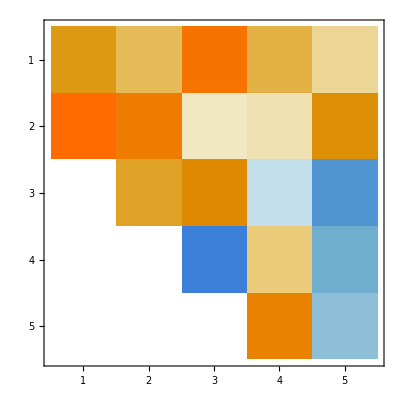
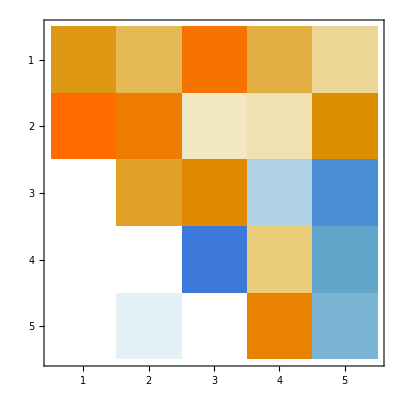

```mathematica
m=5;
A=RandomReal[{-1,1},{m,m}];
{Q,H}=HessenbergDecomposition[A];
Map[Norm,{H-Qᵀ.A.Q, A-Q.H.Qᵀ}]
SignFix1=SparseArray[Band[{1,1}]->Sign[Diagonal[H,-1]],{m,m}];
SignFix2=SparseArray[Band[{2,2}]->Sign[Diagonal[H,-1]],{m,m}];
SignFix=SignFix1.SignFix2;
{QHat,HHat} = {Q.SignFix,H.SignFix};
Map[Norm,{H-QHatᵀ.A.QHat, A-Q.H.Qᵀ}]

Map[MatrixPlot,{H,Qᵀ.A.Q}]
```